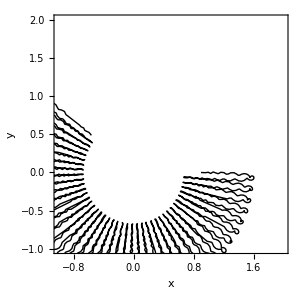
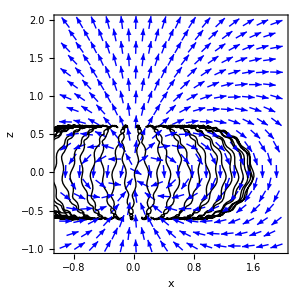
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
q=-1;(*naboj castice*)
vecE={0,0,0};
vecB=10{(3x[t]z[t])/((x[t]^2+y[t]^2+z[t]^2)^(5/2)),(3y[t]z[t])/((x[t]^2+y[t]^2+z[t]^2)^(5/2)),(-(x[t]^2+y[t]^2- 2 z[t]^2))/((x[t]^2+y[t]^2+z[t]^2)^(5/2))};(*kartezsky dipol*)
vecV={vx[t], vy[t], vz[t]};
vecVxB=Cross[vecV,vecB];
rovnice ={(*Lorentz force*)
x'[t]  ==   vx[t],y'[t]  ==   vy[t],z'[t]  ==   vz[t],
vx'[t]==q(vecE[[1]]+vecVxB[[1]]),vy'[t]==q(vecE[[2]]+vecVxB[[2]]),vz'[t]==q(vecE[[3]]+vecVxB[[3]])
};
podminky ={ x[0]  ==0.9, vx[0]==  0.1, y[0]  ==0, vy[0]==0.1,z[0]  ==0.6, vz[0]==0 }; 
draha=NDSolve[{rovnice,podminky},{x,vx,y,vy,z,vz},{t,0,1000}];
(*______________________________________________________________________________________________________________________________*)
{Show[
VectorPlot[{vecB[[1]],vecB[[2]]}/.{x[t]->x,y[t]->y,z[t]->0},{x,-1,2},{y,-1,2},FrameLabel->{x,y},ImageSize->300,VectorStyle->Blue,VectorColorFunction->None],
ParametricPlot[{x[t],y[t]}/.draha,{t,0,1000},PlotRange->{{-1,2},{-1,2}},PlotStyle->{{Black,Thick}}]
],
Show[
VectorPlot[{vecB[[1]],vecB[[3]]}/.{x[t]->x,y[t]->0,z[t]->z},{x,-1,2},{z,-1,2},FrameLabel->{x,z},ImageSize->300,VectorStyle->Blue,VectorColorFunction->None],
ParametricPlot[{x[t],z[t]}/.draha,{t,0,1000},PlotRange->{{-1,2},{-1,2}},PlotStyle->{{Black,Thick}}]
],
ParametricPlot3D[{x[t],y[t],z[t]}/.draha,{t,0,1000},ImageSize->300,PlotRange->{{-1.8,1.5},{-1.8,1.5},{-1.8,1.5}},PlotStyle->{{Black,Thick}}]
}
```

```mathematica
(*podminky z paperu*)
```

{-Graphics-,-Graphics-,-Graphics3D-}

NDSolve::nrnum1: The function value 0.000031275+0.000113238 ⅈ is not a real number when the arguments are {31.4074,0.403772+0.0000171356 ⅈ,1.71281+0. ⅈ,0.845667-0.0000123816 ⅈ,-1.,-1}.

NDSolve::nlnum: The function value $Failed is not a list of numbers with dimensions {3} at {t,lam[t],phi[t],rho[t],s[t],NDSolve`s$48087[t]} = {31.4074,{0.403772+0.0000171356 ⅈ,1.71281+0. ⅈ,0.845667-0.0000123816 ⅈ},{-1.},{-1}}.

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

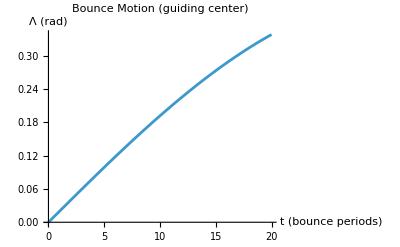

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

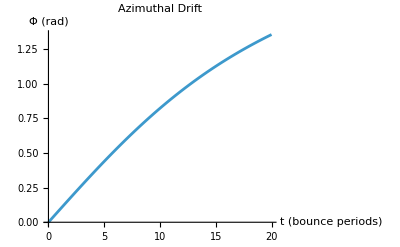

InterpolatingFunction::dmval: Input value {0.0204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* ==========1. CONSTANTS==========*)eps=0.02;    (*small parameter*)
mu=1.0;      (*magnetic moment*)
Bt=2.0;      (*turning point field*)
nu=0.02;     (*bounce frequency νₑ*)
Omega=1.0;   (*cyclotron frequency*)

(* ==========2. FUNCTIONS (all purely numeric)==========*)
B[rho_,lam_]:=Sqrt[1+3 Sin[lam]^2]/rho^3                     (*Eq.3*)
psi[rho_,lam_]:=Cos[lam]^2/rho                                 (*Eq.6*)

bz[lam_]:=(15 Sin[lam]^4+1)/(2 (1+3 Sin[lam]^2)^(3/2))     (*Eq.22*)
dbz[lam_]:=(60 Sin[lam]^3 Cos[lam] (1+3 Sin[lam]^2)-18 Sin[lam] Cos[lam] (15 Sin[lam]^4+1))/(4 (1+3 Sin[lam]^2)^(5/2))

psiStar[rho_,lam_]:=psi[rho,lam]-(eps^2/2) mu bz[lam]         (*Eq.37*)
dPsidRho[rho_,lam_]:=-Cos[lam]^2/rho^2
dPsidLam[rho_,lam_]:=-2 Cos[lam] Sin[lam]/rho-(eps^2/2) mu dbz[lam]

Kcurv[lam_]:=3 (1-Sin[lam]^4)/(1+3 Sin[lam]^2)^(3/2)        (*Eq.8*)

(*Parallel momentum magnitude–avoids complex numbers*)
PparMag[rho_,lam_]:=If[B[rho,lam]<=Bt,Sqrt[Bt-B[rho,lam]],0]

(*B∥*(Eq.31)*)
Bstar[rho_,lam_]:=-1/(rho^2 Cos[lam] Sqrt[1+3 Sin[lam]^2])*(2 Sin[lam] dPsidLam[rho,lam]+rho Cos[lam] dPsidRho[rho,lam])

(* ==========3. ODE SYSTEM with discrete sign s(t)==========*)
odes={rho'[t]==(nu*s[t]*PparMag[rho[t],lam[t]])/(rho[t]^2 Cos[lam[t]] Bstar[rho[t],lam[t]])*(-dPsidLam[rho[t],lam[t]]),lam'[t]==(nu*s[t]*PparMag[rho[t],lam[t]])/(rho[t]^2 Cos[lam[t]] Bstar[rho[t],lam[t]])*(+dPsidRho[rho[t],lam[t]]),phi'[t]==(nu/(2 Omega))*(B[rho[t],lam[t]]+2 PparMag[rho[t],lam[t]]^2)/Bstar[rho[t],lam[t]]*Kcurv[lam[t]]/(rho[t]^2 Cos[lam[t]]^2)};

(*Flip sign at turning points*)
events={WhenEvent[B[rho[t],lam[t]]>=Bt,s[t]->-s[t]]};

(*Initial conditions*)
init={rho[0]==1.0,lam[0]==0.0,phi[0]==0.0,s[0]==-1};

(*Solve–s is a discrete variable,no derivative for s*)
sol=NDSolve[{odes,events,init},{rho,lam,phi},{t,1,500},DiscreteVariables->{s}];(*???*)

(* ==========4. PLOTS==========*)
Plot[lam[t]/. sol,{t,0,20},AxesLabel->{"t (bounce periods)","Λ (rad)"},PlotLabel->"Bounce Motion (guiding center)"]

Plot[phi[t]/. sol,{t,0,20},AxesLabel->{"t (bounce periods)","Φ (rad)"},PlotLabel->"Azimuthal Drift"]
ParametricPlot3D[{rho[t],lam[t],phi[t]}/.sol,{t,0,1000},ImageSize->300,PlotRange->{{-1.8,1.5},{-1.8,1.5},{-1.8,1.5}},PlotStyle->{{Black,Thick}}]
```

```mathematica
(*attemp 2*)
```

```mathematica
(*R - 3 eqs x,y,z + dv parallel to B - 1 eq *)
```

ClearAll